```mathematica
;;;
```

Last updated:   Tue 11 Jul 2023
Author:   Martins Dogo

## Synonyms

## Functions

```mathematica
Clear[toGrid,getSynonyms,getBroaderTerms,getNearTerms]

toGrid[items_,opts___]:=Style[Framed[Grid[items,opts,Dividers->{False,All},Alignment->Left,Spacings->{2, 2}],FrameMargins->20,FrameStyle->None,Background->GrayLevel[.9]],FontFamily->"Source Serif Pro"];

getSynonyms[words_String|words_List]:=getSynonyms[words]=ToLowerCase@AlphabeticSort@Flatten[Cases[WordData[#,"Synonyms"],({w_,pos_/;pos=="Verb",def_}->syn__)->syn,∞]&/@Flatten[{words}]];

getBroaderTerms[words_String|words_List]:=ToLowerCase@AlphabeticSort@Flatten[Cases[WordData[#,"BroaderTerms"],({w_,pos_/;pos=="Verb",def_}->syn__)->syn,∞]&/@Flatten[{words}]];

getNearTerms[words_String|words_List]:=With[{w=Flatten[{words}]},ToLowerCase@AlphabeticSort[Flatten@DeleteDuplicates[Join[getBroaderTerms[w],getSynonyms[w]]]]];
```

## Words

```mathematica
Names["*Word*"]
```

{AutoItalicWords,AutoStyleWords,DictionaryWordQ,GroupElementFromWord,GroupElementToWord,MaxWordGap,NullWords,RandomWord,TextWords,TokenWords,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,$SystemWordLength}

```mathematica
toGrid[{#,Information[#,"Usage"]}&/@{WordData,WordDefinition,WordFrequency}]
```

WordData | WordData[word,property] gives the specified property for the English word "word".
WordData[word] gives a list of full word specifications representing possible uses and senses of "word".
WordData[wordspec,property] gives a property for a particular word specification.
WordDefinition | WordDefinition[word] gives the dictionary definitions available for "word".
WordFrequency | WordFrequency[text,word] gives the frequency of word in text.
WordFrequency[text,{word_1,word_2,…}] gives an association of the frequencies of each of the word_i.

```mathematica
WordData["word","Properties"]
```

{AmericanSpelling,Antonyms,BaseAdjective,BaseForm,BaseNoun,BritishSpelling,BroaderTerms,CausesTerms,CompositeTerms,ConceptWeight,ConsequencesTerms,Definitions,DerivedAdjectives,DerivedAdverbs,EntailedTerms,Examples,GeographicDomain,Hyphenation,InflectedForms,MaterialTerms,MorphologicalDerivatives,MorphologicalSource,NarrowerTerms,PartsOfSpeech,PartTerms,PhoneticForm,PorterStem,SentenceFrames,SimilarAdjectives,SimilarVerbs,SubsetTerms,SupersetTerms,Synonyms,UsageField,UsageType,WholeTerms,WordNetID}

```mathematica
{WordData["admonish","Examples"]}//Transpose//toGrid
```

{admonish,Verb,Criticize}→{He admonished the child for his bad behavior}
{admonish,Verb,Rede}→{}
{admonish,Verb,Warn}→{}

```mathematica
verbs=WordData[All,"Verb"];
%//Short
Length@verbs
```

{aah,abacinate,abandon,abase,«11523»,zonk out,zoom,zoom along,zoom in}

11531

## Graphs

### Questions

```mathematica
(*
1. Are there words (verbs), the NestGraph of which, contain a Hamiltolian or Eulerian cycle?;
2. [Original question I had] How about an alphabetically sorted cycle (e.g. admonish -> beseech -> chide)?;
3. Could traversal through the synonym/broader terms nest graph of a given word (verb) eventually lead to an antonym of that word?;
4. Which verb has the longest path in a NestGraph of synonyms/broader terms?; 
*)
```

### Synonyms

```mathematica
(* synonyms terms *)
getSynonyms["code"]
```

{cipher,cypher,encipher,encrypt,inscribe,write in code}

```mathematica
(* why nest list isn't a good approach --> we can obtain a word or more for all English alphabets, but a lot of them are not even remotely synonymous *)
groupedByFirstLetter=GroupBy[AlphabeticSort@DeleteDuplicates@Flatten@NestList[getNearTerms,"allow",5],First@Characters@ToLowerCase[#]&];
toGrid@Transpose[{Keys@groupedByFirstLetter,Short[#,1]&/@Values[groupedByFirstLetter]}]
```

a | {abandon,abase,abash,abate,«291»,await,awake,awaken,award}
b | {babble,babble out,baby,baby-sit,«447»,buy up,buzz,buzz off,bypass}
c | {ca-ca,cabal,cabbage,cache,«668»,cut through,cut up,cycle,cypher}
d | {dally,damage,damn,damp,«496»,dust,dwarf,dwell,dye}
e | {earmark,earn,earth up,ease,ease off,«294»,exudate,exude,exult,exuviate}
f | {fabricate,face,face up,face-lift,«343»,furrow,further,fuse,fuss}
g | {gabble,gag,gage,gain,gain ground,«254»,guttle,guy,gybe,gyp,gyrate}
h | {habilitate,habituate,hack,«208»,hypothecate,hypothesise,hypothesize}
i | {ideate,identify,idle,idolise,«211»,itch,itemise,itemize,iterate}
j | {jab,jack off,jactitate,jade,«53»,junketeer,justify,jut,jut out}
k | {keel,keep,keep abreast,keep an eye on,«48»,kotow,kowtow,kvetch}
l | {label,labialise,labialize,labor,«204»,lure,lurk,luxate,luxuriate}
m | {macerate,machinate,maculate,magnetise,«251»,mutter,muzzle,mystify}
n | {nab,nag,nail,nail down,name,«57»,nurse,nurture,nutrify,nuzzle}
o | {o.k.,obey,object,objectify,«134»,oxygenate,oxygenise,oxygenize}
p | {pace,pacify,pack,pack together,«496»,putter around,puzzle,puzzle out}
q | {quail,quail at,quake,qualify,quantify,«21»,quit,quiver,quiz,quote}
r | {race,rack,rack up,racket,radiate,«422»,rush out,rust,rustle,rut}
s | {sabotage,sack,sack out,sack up,«820»,systematize,systemise,systemize}
t | {table,tabularise,tabularize,tabulate,«374»,typeset,typewrite,typify}
u | {ululate,unbend,unblock,unbosom,«79»,usurp,utilise,utilize,utter}
v | {vacate,vacillate,vagabond,validate,«60»,voyage,vulgarise,vulgarize}
w | {wad,wade,waffle,wage,wager,«163»,write out,write up,writhe,wrong}
x | {xerox}
y | {yack,yack away,yammer,yank,yap away,«5»,yell,yen,yield,yoke,yowl}
z | {zap,zip,zip up,zipper,zonk out}

```mathematica
(* n nest graph of synonyms *)
ng=NestGraph[getNearTerms,"program",4,DirectedEdges->True(*,VertexLabels->Automatic,PlotTheme->"Monochrome",VertexSize->0.05,EdgeStyle->Opacity[.2],GraphLayout->"BalloonEmbedding"*)];
{VertexCount@ng,EdgeCount@ng}
```

{122,176}

```mathematica
(* communities of synonyms *)
CommunityGraphPlot[ng,FindGraphCommunities[ng],VertexSize->0.2,VertexLabels->Automatic,ImageSize->650]
```

-Graphics-

```mathematica
(* cycle-related graph properties *)
Highlighted[{AcyclicGraphQ[ng],HamiltonianGraphQ[ng],EulerianGraphQ[ng]}]
```

{False,False,False}

```mathematica
(* find cycles of all types and lengths *)
cycles=FindCycle[ng]
```

{{program->programme,programme->program}}

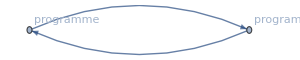

```mathematica
(* graph cycles *)
Graph[#,VertexLabels->"Name",ImageSize->300]&/@cycles
```